```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

## -1/3 < m < 0

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

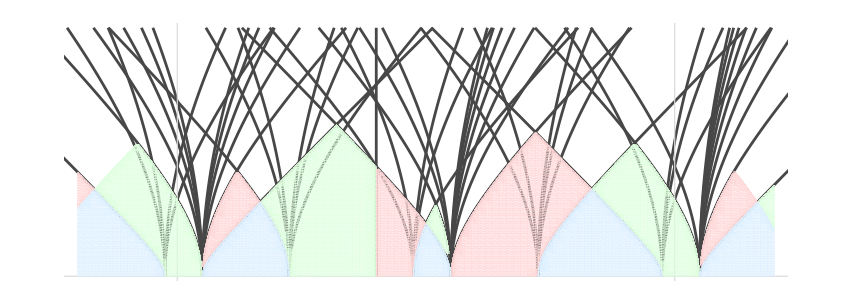

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=-1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

plt1=Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

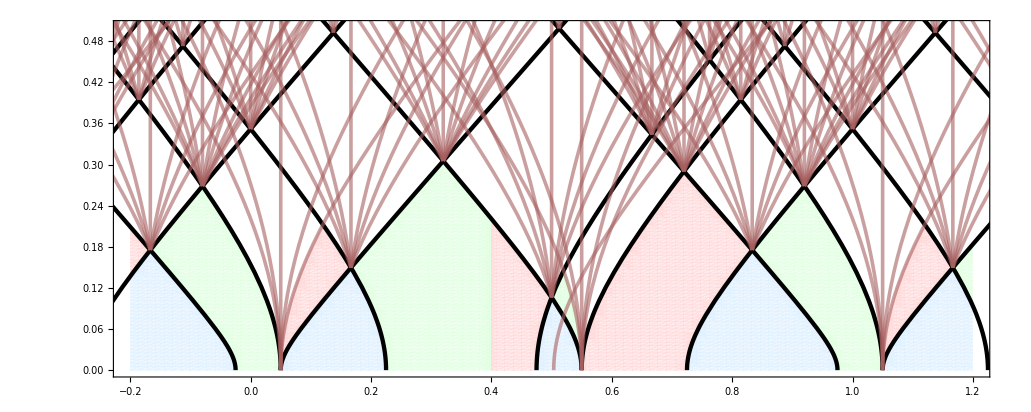

```mathematica
Show[domainI,domainII,domainBr,temp,AspectRatio->Automatic]
```

## 0 < m < 1/3

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{1,0},{2,1},{3,2},{4,2},{5,3}}

{{0,0},{1,1},{2,2},{3,2},{4,3}}

{{0,0},{1,1},{2,2},{3,2},{4,3}}

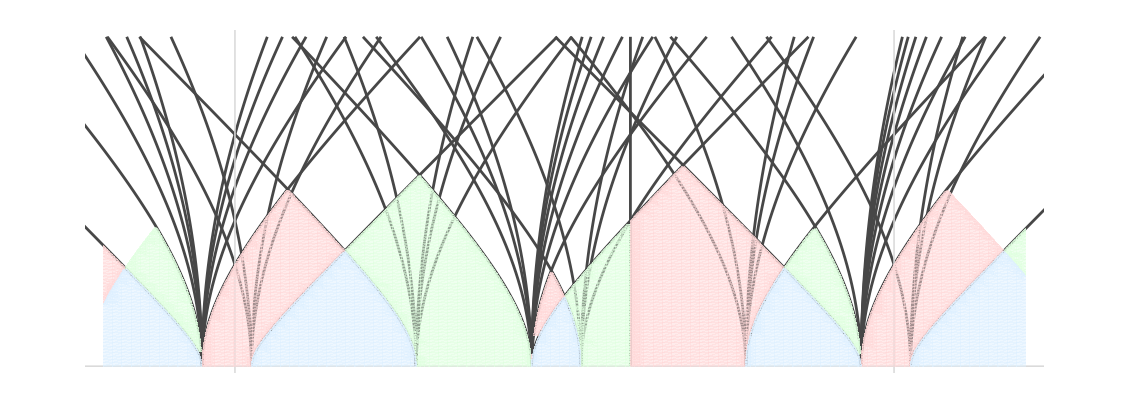

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=1/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Echo@ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

## 1/3 < m < 2/3

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

{{1,1},{2,1},{3,2},{4,3},{5,3}}

{{0,1},{1,1},{2,2},{3,3},{4,3}}

{{0,1},{1,1},{2,2},{3,3},{4,3}}

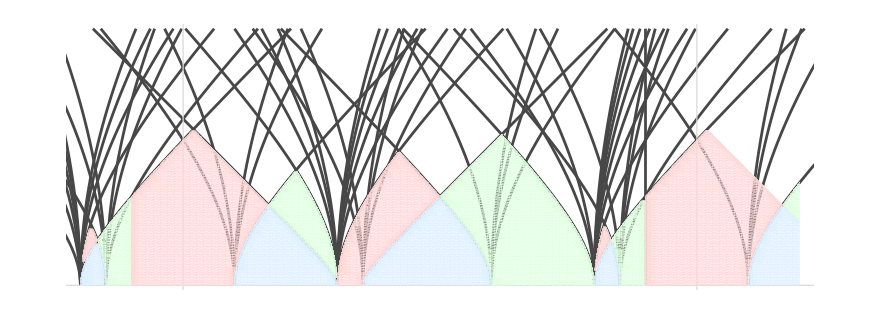

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=4/10, psi=0, xmin=-0.2, xmax=1.2, tmax=0.5},
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
(* add Rank 0 sheaf *)
AppendTo[charges,GV[0,-1,-1/2]];

(* compute rays and captions *)
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];

(* compute quiver domains *)
CollDom[Coll_, Color_]:=Module[{possibleSpecParams},
possibleSpecParams = Echo@ListSpecFlows[Coll, psi, m, 12, xmin, xmax, tmax];
Table[QuiverDomain[SpectralFlow[Coll, spec],psi,m,PlotStyle->Color,PlotRange->{{xmin,xmax},{0,tmax}}, PlotPoints->100], {spec,possibleSpecParams}]
];
PrintTemporary["Computing domainI"];
domainI = CollDom[CollArcaraI, LightGreen];
PrintTemporary["Computing domainII"];
domainII = CollDom[CollArcaraII, LightRed];
PrintTemporary["Computing domainBr"];
domainBr = CollDom[CollBridgeland, LightBlue];

Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domainI,
domainII,
domainBr
]
]
```

```mathematica
SpectralFlow[GV[0,-1,-1/2]/.repCh,{-3,-2}]
```

{0,0,-1,1/2}

```mathematica
Ch[0,0]-Ch[0,1]/.repCh
```

{0,0,-1,1/2}

```mathematica
With[{m=2/5},Flatten@Table[k+{m/4, (m+1)/4, (1-m)/2, (m+2)/4, m+1/2, (m+3)/4, 1-m/2}, {k,0,0}]]
```

{1/10,7/20,3/10,3/5,9/10,17/20,4/5}

```mathematica
{m/4, (m+1)/4, (1-m)/2, (m+2)/4, m+1/2, (m+3)/4, 1-m/2}
SortBy[%, #/.{m->2/5}&]
```

{m/4,(1+m)/4,(1-m)/2,(2+m)/4,1/2+m,(3+m)/4,1-m/2}

{m/4,(1-m)/2,(1+m)/4,(2+m)/4,1-m/2,(3+m)/4,1/2+m}

```mathematica
DSZ[Ch[1,1],-Ch[0,1]]/.repCh
```

2

```mathematica
DSZ[Ch[2,1],-Ch[0,1]]/.repCh
```

4

```mathematica
ChernToCh[2Ch[1,1]-Ch[0,1]/.repCh]
```

Ch[2,1]

```mathematica
DSZ[Ch[1,1],-Ch[2,2]]/.repCh
```

-3

```mathematica
DSZ[Ch[3,2],-Ch[2,2]]/.repCh
```

2

```mathematica
SpectralFlow[{0,0,1,ch2},{3k,2k}]
```

{0,0,1,ch2+k}

## Redo

#### -1/3 < m < 0

```mathematica
Needs["MaTeX`"];
myHex="47081b";
SetOptions[MaTeX,"Preamble"->{"\\usepackage[T1]{fontenc}","\\usepackage{lmodern}","\\usepackage{xcolor}","\\definecolor{gamcolor}{HTML}{"<>ToUpperCase[myHex]<>"}"}];
```

```mathematica
(*Example usage*)
MaTeX["\\textcolor{gamcolor}{\\textbf{Hello from amsart (11pt)}}"]
```

-Graphics-

```mathematica
ClearAll[AsBr,AsAI,AsAII];
AsBr[m_]:=<|"Coll"->CollBridgeland, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightBlue|>;
AsAI[m_]:=<|"Coll"->CollArcaraI, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-3)/3]}, {mf,1,5}], "Color"->LightGreen|>;
AsAII[m_]:=<|"Coll"->CollArcaraII, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightRed|>;
```

```mathematica
MakeDomain[AsColl_, m_]:=Table[QDomain[SpectralFlow[AsColl["Coll"]/.repCh, spec], m,spec, PlotStyle->Directive[AsColl["Color"], Opacity[.7]], BoundaryStyle->Transparent, PlotPoints->100], {spec, AsColl["SpectralFlows"]}];
```

```mathematica
ticks=Thread[{#/.m->-1/10, MaTeX[Simplify[#]]}]&@Flatten[Table[{(m+k)/4, (k-m)/2, -1/2-k+m}, {k,-5,5}]];
```

```mathematica
With[{m=-1/10, psi=0, coll=CollInitial[[3]], L=5, xmin=-1, xmax=2},
charges=Flatten[Table[s gam/.{Ch[p_,q_]:>Ch[p+3k,q+2k]},{gam, coll},{k,-L,L},{s,{-1,1}}]];
charges=Join[charges,Table[GV[0,1,-1/2-k], {k,-L,L}]];
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];

othercharges=Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]];
othercharges=Select[othercharges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&&!MemberQ[charges,#]&];
othercharges=Join[othercharges, {GV[1,0,0], GV[1,0,1], GV[1,0,2]}];
otherrays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, othercharges}];

dBr=MakeDomain[AsBr[m],m];
dAI=MakeDomain[AsAI[m],m];
dAII=MakeDomain[AsAII[m],m];
]
```

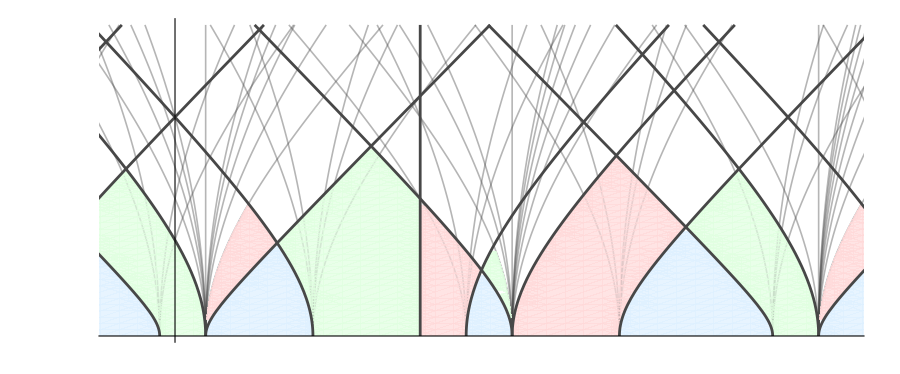

```mathematica
plt=Show[{
ParametricPlot[otherrays, {t,0,0.5},
PlotStyle->Directive[Thickness[.0013],RGBColor[0.28, 0.28, 0.28], Opacity[.4]]
],
dBr,
dAI,
dAII,
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28]
](*,
Graphics[{Red, GamLabel[-Ch[-1,-1], -1/10, 0, "\\mathcal{O}(-1,-1)[1]", .4]}]*)
},
PlotRange->{{-.1, 1.1},{0,0.5}},
AspectRatio->Automatic,
Frame->False,
Axes->{True,False},
Ticks->{ticks,None},
ImageSize->900
]
```

```mathematica
(*FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "LVRasterize_m_m1_10.pdf"], %]*)
```

/Users/rishi/Developer/localf1/figures/LargeVolume/LVRasterize_m_m1_10.pdf

```mathematica
GamLabel[gam_, m_, psi_, string_, t0_]:=Module[{r=(gam/.repCh)[[1]]},Text[MaTeX["\\textcolor{gamcolor}{"<>string<>"}"], {Rays[gam/.repCh, #,psi,m], #}&[t0], {0,-1}, -Sign[If[r!=0,r,-1]]Normalize[{D[Rays[gam/.repCh, t,psi,m],t]/.{t->t0}, 1}]]];
```

```mathematica
labels=With[{m=-1/10,psi=0},{
GamLabel[Ch[0,0], m, psi, "\\mathcal{O}(0,0)", .1],
GamLabel[Ch[1,0], m, psi, "\\mathcal{O}(1,0)", .33],
GamLabel[Ch[1,1], m, psi, "\\mathcal{O}(1,1)", .43],
GamLabel[-Ch[-1,-1], m, psi, "\\mathcal{O}(-1,-1)[1]", .4],
GamLabel[Ch[2,1], m, psi, "\\mathcal{O}(2,1)", .4],
GamLabel[-Ch[0,0], m, psi, "\\mathcal{O}(0, 0)[1]", .35],
GamLabel[Ch[3,2], m, psi, "\\mathcal{O}(3, 2)", .44],
GamLabel[-Ch[1,0], m, psi, "\\mathcal{O}(1, 0)[1]", .4],
GamLabel[-Ch[1,1], m, psi, "\\mathcal{O}(1, 1)[1]", .43],
GamLabel[Ch[4,2], m, psi, "\\mathcal{O}(4, 2)", .35],
GamLabel[Ch[4,3], m, psi, "\\mathcal{O}(4, 3)", .4],
GamLabel[-Ch[2,1], m, psi, "\\mathcal{O}(2, 1)[1]", .4],
GamLabel[-Ch[3,2], m, psi, "\\mathcal{O}(3, 2)[1]", .1],
GamLabel[GV[0,1,1/2], m, psi, "GV\\left(0,1,\\tfrac12\\right)", .1],
(* Quiver domains for CollBridgeland *)
Text[MaTeX["\\mathcal{C}"], {-.12,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(1,1)"], {.14,.04}],
Text[Column[MaTeX/@{"\\mathcal{C}\\otimes","\\mathcal{O}(2,1)"},Center, -.1], {.51, .04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(3,2)"], {.84,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(4,3)"], {1.12,.03}],
(* Quiver domains for CollArcaraI *)
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(1,0)"], {-.07,.16}],
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(2,1)"], {.3,.06}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(3,1)"},Center, -.1], {.53,.117}],
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(4,2)"], {.97,.1}],
(* Quiver domains for CollArcaraII *)
Text[Column[MaTeX/@{"\\mathcal{C}'\\otimes","\\mathcal{O}(1,1)"},Center, -.1], {0.123,.16}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(2,1)"], {.45,.1}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(3,2)"], {.67,.1}],
Text[Column[MaTeX/@{"\\mathcal{C}'\\otimes","\\mathcal{O}(4,3)"},Center, -.1], {1.12,.17}]
}];
plt1=Show[plt, Graphics[labels]]
```

-Graphics-

```mathematica
FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt1, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "Ras_LV_m_m1_10.pdf"], %]
```

/Users/rishi/Developer/localf1/figures/LargeVolume/Ras_LV_m_m1_10.pdf

```mathematica
Ch[1,0]-Ch[0,0]/.repCh
```

{0,1,0,0}

#### 0 < m < 1/3

```mathematica
Needs["MaTeX`"];
myHex="47081b";
SetOptions[MaTeX,"Preamble"->{"\\usepackage[T1]{fontenc}","\\usepackage{lmodern}","\\usepackage{xcolor}","\\definecolor{gamcolor}{HTML}{"<>ToUpperCase[myHex]<>"}"}];
```

```mathematica
(*Example usage*)
MaTeX["\\textcolor{gamcolor}{\\textbf{Hello from amsart (11pt)}}"]
```

-Graphics-

```mathematica
ClearAll[AsBr,AsAI,AsAII];
AsBr[m_]:=<|"Coll"->CollBridgeland, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightBlue|>;
AsAI[m_]:=<|"Coll"->CollArcaraI, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-3)/3]}, {mf,1,5}], "Color"->LightGreen|>;
AsAII[m_]:=<|"Coll"->CollArcaraII, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightRed|>;
```

```mathematica
MakeDomain[AsColl_, m_]:=Table[QDomain[SpectralFlow[AsColl["Coll"]/.repCh, spec], m,spec, PlotStyle->Directive[AsColl["Color"], Opacity[.7]], BoundaryStyle->Transparent, PlotPoints->100], {spec, AsColl["SpectralFlows"]}];
```

```mathematica
ticks=Thread[{#/.m->1/10, MaTeX[Simplify[#]]}]&@Flatten[Table[{(m+k)/4, (k-m)/2, -1/2-k+m}, {k,-5,5}]];
```

```mathematica
With[{m=1/10, psi=0, coll=CollInitial[[1]], L=5, xmin=-1, xmax=2},
charges=Flatten[Table[s gam/.{Ch[p_,q_]:>Ch[p+3k,q+2k]},{gam, coll},{k,-L,L},{s,{-1,1}}]];
charges=Join[charges,Table[GV[0,1,-1/2-k], {k,-L,L}]];
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];

othercharges=Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]];
othercharges=Select[othercharges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&&!MemberQ[charges,#]&];
othercharges=Join[othercharges, {GV[1,0,0], GV[1,0,1], GV[1,0,2]}];
otherrays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, othercharges}];

dBr=MakeDomain[AsBr[m],m];
dAI=MakeDomain[AsAI[m],m];
dAII=MakeDomain[AsAII[m],m];
]
```

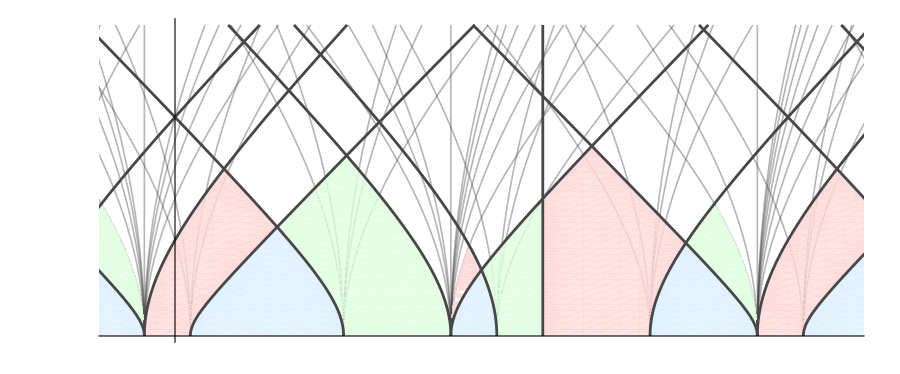

```mathematica
plt=Show[{
ParametricPlot[otherrays, {t,0,0.5},
PlotStyle->Directive[Thickness[.0013],RGBColor[0.28, 0.28, 0.28], Opacity[.4]]
],
dBr,
dAI,
dAII,
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28]
](*,
Graphics[{Red, GamLabel[-Ch[-1,-1], -1/10, 0, "\\mathcal{O}(-1,-1)[1]", .4]}]*)
},
PlotRange->{{-.1, 1.1},{0,0.5}},
AspectRatio->Automatic,
Frame->False,
Axes->{True,False},
Ticks->{ticks,None},
ImageSize->900
]
```

```mathematica
(*FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "LVRasterize_m_m1_10.pdf"], %]*)
```

/Users/rishi/Developer/localf1/figures/LargeVolume/LVRasterize_m_m1_10.pdf

```mathematica
GamLabel[gam_, m_, psi_, string_, t0_]:=Module[{r=(gam/.repCh)[[1]]},Text[MaTeX["\\textcolor{gamcolor}{"<>string<>"}"], {Rays[gam/.repCh, #,psi,m], #}&[t0], {0,-1}, -Sign[If[r!=0,r,-1]]Normalize[{D[Rays[gam/.repCh, t,psi,m],t]/.{t->t0}, 1}]]];
```

```mathematica
labels=With[{m=1/10,psi=0},{
GamLabel[Ch[0,0], m, psi, "\\mathcal{O}(0,0)", .08],
GamLabel[Ch[1,0], m, psi, "\\mathcal{O}(1,0)", .33],
GamLabel[Ch[1,1], m, psi, "\\mathcal{O}(1,1)", .43],
GamLabel[-Ch[-1,-1], m, psi, "\\mathcal{O}(-1,-1)[1]", .3],
GamLabel[-Ch[-1,0], m, psi, "\\mathcal{O}(-1,0)[1]", .33],
GamLabel[Ch[2,1], m, psi, "\\mathcal{O}(2,1)", .35],
GamLabel[Ch[2,2], m, psi, "\\mathcal{O}(2,2)", .25],
GamLabel[-Ch[2,2], m, psi, "\\mathcal{O}(2,2)[1]", .2],
GamLabel[-Ch[0,0], m, psi, "\\mathcal{O}(0, 0)[1]", .4],
GamLabel[Ch[3,2], m, psi, "\\mathcal{O}(3, 2)", .25],
GamLabel[-Ch[1,1], m, psi, "\\mathcal{O}(1, 1)[1]", .43],
GamLabel[Ch[4,3], m, psi, "\\mathcal{O}(4, 3)", .4],
GamLabel[-Ch[2,1], m, psi, "\\mathcal{O}(2, 1)[1]", .4],
GamLabel[-Ch[3,2], m, psi, "\\mathcal{O}(3, 2)[1]", .1],
GamLabel[GV[0,1,1/2], m, psi, "GV\\left(0,1,\\tfrac12\\right)", .3],
(* Quiver domains for CollBridgeland *)
Text[MaTeX["\\mathcal{C}"], {-.13,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(1,1)"], {.16,.04}],
Text[Column[MaTeX/@{"\\mathcal{C}\\otimes","\\mathcal{O}(2,2)"},Center, -.1], {.49, .04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(3,2)"], {.86,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(4,3)"], {1.11,.03}],
(* Quiver domains for CollArcaraI *)
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(1,0)"}, Center, -.1], {-.12,.16}],
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(2,1)"], {.35,.06}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(3,2)"},Center, -.1], {.56,.11}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(4,2)"}, Center, -.1], {.88,.15}],
(* Quiver domains for CollArcaraII *)
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(1,1)"], {0.08,.17}],
Text[Column[MaTeX/@{"\\mathcal{C}'\\otimes", "\\mathcal{O}(2,2)"}, Center, -.1], {.47,.11}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(3,2)"], {.7,.1}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(4,3)"], {1.08,.17}](**)
}];
plt1=Show[plt, Graphics[labels]]
```

-Graphics-

```mathematica
FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt1, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "Ras_LV_m_1_10.pdf"], %]
```

/Users/rishi/Developer/localf1/figures/LargeVolume/Ras_LV_m_1_10.pdf

```mathematica
Ch[0,0]-Ch[-1,0]/.repCh
```

{0,1,0,0}

```mathematica
Ch[2,1]-Ch[1,1]/.repCh
```

{0,1,0,1}

#### 1/3 < m < 2/3

```mathematica
Needs["MaTeX`"];
myHex="47081b";
SetOptions[MaTeX,"Preamble"->{"\\usepackage[T1]{fontenc}","\\usepackage{lmodern}","\\usepackage{xcolor}","\\definecolor{gamcolor}{HTML}{"<>ToUpperCase[myHex]<>"}"}];
```

```mathematica
(*Example usage*)
MaTeX["\\textcolor{gamcolor}{\\textbf{Hello from amsart (11pt)}}"]
```

-Graphics-

```mathematica
ClearAll[AsBr,AsAI,AsAII];
AsBr[m_]:=<|"Coll"->CollBridgeland, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightBlue|>;
AsAI[m_]:=<|"Coll"->CollArcaraI, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-3)/3]}, {mf,1,5}], "Color"->LightGreen|>;
AsAII[m_]:=<|"Coll"->CollArcaraII, "SpectralFlows"->Table[{mf, Ceiling[(2mf+3m-1)/3]}, {mf,0,4}], "Color"->LightRed|>;
```

```mathematica
MakeDomain[AsColl_, m_]:=Table[QDomain[SpectralFlow[AsColl["Coll"]/.repCh, spec], m,spec, PlotStyle->Directive[AsColl["Color"], Opacity[.7]], BoundaryStyle->Transparent, PlotPoints->100], {spec, AsColl["SpectralFlows"]}];
```

```mathematica
ticks=Thread[{#/.m->4/10, MaTeX[Simplify[#]]}]&@Flatten[Table[{(m+k)/4, (k-m)/2, -1/2-k+m}, {k,-5,5}]];
```

```mathematica
With[{m=4/10, psi=0, coll=CollInitial[[2]], L=5, xmin=-1, xmax=2},
charges=Flatten[Table[s gam/.{Ch[p_,q_]:>Ch[p+3k,q+2k]},{gam, coll},{k,-L,L},{s,{-1,1}}]];
charges=Join[charges,Table[GV[0,1,-1/2-k], {k,-L,L}]];
charges=Select[charges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&];
rays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, charges}];

othercharges=Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]];
othercharges=Select[othercharges, xmin<=Rays[#/.repCh,0,psi,m]<=xmax&&!MemberQ[charges,#]&];
othercharges=Join[othercharges, {GV[1,0,0], GV[1,0,1], GV[1,0,2]}];
otherrays = Table[Tooltip[{Rays[g/.repCh, t,psi,m], t}, g], {g, othercharges}];

dBr=MakeDomain[AsBr[m],m];
dAI=MakeDomain[AsAI[m],m];
dAII=MakeDomain[AsAII[m],m];
]
```

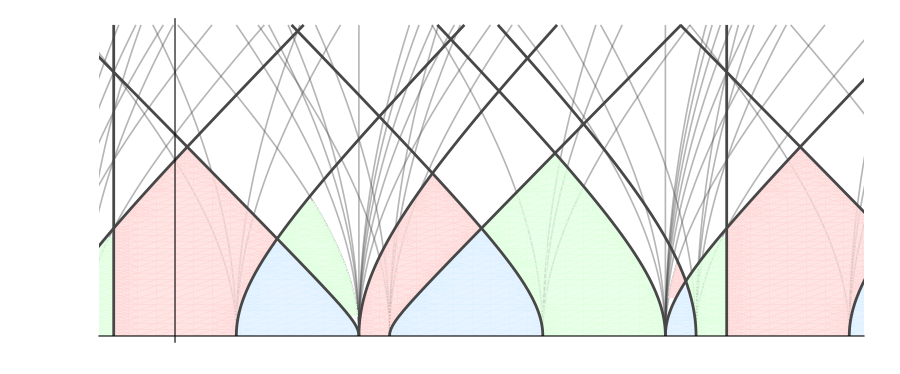

```mathematica
plt=Show[{
ParametricPlot[otherrays, {t,0,0.5},
PlotStyle->Directive[Thickness[.0013],RGBColor[0.28, 0.28, 0.28], Opacity[.4]]
],
dBr,
dAI,
dAII,
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28]
](*,
Graphics[{Red, GamLabel[-Ch[-1,-1], -1/10, 0, "\\mathcal{O}(-1,-1)[1]", .4]}]*)
},
PlotRange->{{-.1, 1.1},{0,0.5}},
AspectRatio->Automatic,
Frame->False,
Axes->{True,False},
Ticks->{ticks,None},
ImageSize->900
]
```

```mathematica
(*FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "LVRasterize_m_m1_10.pdf"], %]*)
```

/Users/rishi/Developer/localf1/figures/LargeVolume/LVRasterize_m_m1_10.pdf

```mathematica
GamLabel[gam_, m_, psi_, string_, t0_]:=Module[{r=(gam/.repCh)[[1]]},Text[MaTeX["\\textcolor{gamcolor}{"<>string<>"}"], {Rays[gam/.repCh, #,psi,m], #}&[t0], {0,-1}, -Sign[If[r!=0,r,-1]]Normalize[{D[Rays[gam/.repCh, t,psi,m],t]/.{t->t0}, 1}]]];
```

```mathematica
labels=With[{m=4/10,psi=0},{
GamLabel[Ch[0,0], m, psi, "\\mathcal{O}(0,0)", .08],
GamLabel[Ch[1,0], m, psi, "\\mathcal{O}(1,0)", .33],
GamLabel[Ch[1,1], m, psi, "\\mathcal{O}(1,1)", .25],
GamLabel[-Ch[-1,0], m, psi, "\\mathcal{O}(-1,0)[1]", .37],
GamLabel[-Ch[0,1], m, psi, "\\mathcal{O}(0,1)[1]", .35],
GamLabel[Ch[2,2], m, psi, "\\mathcal{O}(2,2)", .22],
GamLabel[-Ch[2,2], m, psi, "\\mathcal{O}(2,2)[1]", .35],
GamLabel[-Ch[0,0], m, psi, "\\mathcal{O}(0, 0)[1]", .2],
GamLabel[Ch[3,2], m, psi, "\\mathcal{O}(3, 2)", .2],
GamLabel[Ch[3,3], m, psi, "\\mathcal{O}(3, 3)", .28],
GamLabel[-Ch[1,1], m, psi, "\\mathcal{O}(1, 1)[1]", .265],
GamLabel[Ch[4,3], m, psi, "\\mathcal{O}(4, 3)", .27],
GamLabel[-Ch[3,2], m, psi, "\\mathcal{O}(3, 2)[1]", .1],
GamLabel[GV[0,1,-1/2], m, psi, "GV\\left(0,1,-\\tfrac12\\right)", .25],
GamLabel[GV[0,1,1/2], m, psi, "GV\\left(0,1,\\tfrac12\\right)", .22],
(* Quiver domains for CollBridgeland *)
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(1,1)"], {.19,.04}],
Text[MaTeX["\\mathcal{C}\\otimes\\mathcal{O}(2,2)"], {.49, .04}],
Text[Column[MaTeX/@{"\\mathcal{C}\\otimes","\\mathcal{O}(3,3)"}, Center, -.1], {.826,.03}],
Text[Column[MaTeX/@{"\\mathcal{C}\\otimes","\\mathcal{O}(4,3)"}, Center, -.1], {1.14,.04}],
(* Quiver domains for CollArcaraI *)
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(1,1)"}, Center, -.1], {-.13,.09}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(2,1)"}, Center, -.1], {.22,.16}],
Text[MaTeX["\\mathcal{C}''\\otimes\\mathcal{O}(3,2)"], {.66,.11}],
Text[Column[MaTeX/@{"\\mathcal{C}''\\otimes","\\mathcal{O}(4,3)"}, Center, -.1], {.87,.09}],
(* Quiver domains for CollArcaraII *)
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(1,1)"], {0.01,.1}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(2,2)"], {.41,.15}],
Text[Column[MaTeX/@{"\\mathcal{C}'\\otimes","\\mathcal{O}(3,3)"}, Center,-.1], {.78,.12}],
Text[MaTeX["\\mathcal{C}'\\otimes\\mathcal{O}(4,3)"], {1.01,.1}](**)
}];
plt1=Show[plt, Graphics[labels]]
```

-Graphics-

```mathematica
FigDir="/Users/rishi/Developer/localf1/figures/LargeVolume";
Rasterize[plt1, ImageSize->900, ImageResolution->300];
Export[FileNameJoin[FigDir, "Ras_LV_m_4_10.pdf"], %]
```

/Users/rishi/Developer/localf1/figures/LargeVolume/Ras_LV_m_4_10.pdf

```mathematica
Ch[0,0]-Ch[-1,0]/.repCh
```

{0,1,0,0}

```mathematica
Ch[2,1]-Ch[1,1]/.repCh
```

{0,1,0,1}

## XY Plane

```mathematica
Needs["MaTeX`"];
myHex="47081b";
SetOptions[MaTeX,"Preamble"->{"\\usepackage[T1]{fontenc}","\\usepackage{lmodern}","\\usepackage{xcolor}","\\definecolor{gamcolor}{HTML}{"<>ToUpperCase[myHex]<>"}"}];
```

```mathematica
ch=Flatten@ChernToCh[Table[SpectralFlow[CollInitial[[3]]/.repCh, {3k,2k}], {k,-3,3}]];
in=Simplify@Table[NaiveIntersection[-ch[[k]]/.repCh, ch[[k+1]]/.repCh, m], {k,1,Length[ch]-1}];
lines[m_]=Table[Line[{in[[k]], in[[k+1]]}], {k, 1, Length[in]-1}];
```

```mathematica
labels[m_]=Simplify[Table[Text[With[{tmp=(ch[[k+1]]/.repCh)[[{2,3}]]},MaTeX["\\textcolor{gamcolor}{\\mathcal{O}("<>ToString[tmp[[1]]]<>","<>ToString[tmp[[2]]]<>")}"]], (in[[k]]+in[[k+1]])/2, {0,1.5}, (in[[k+1]]-in[[k]])/{1,14/3}],{k, 1, Length[in]-1}]];
```

```mathematica
XYFan[ch1_, ch2_,m_, Nr_:10]:=Module[{kap,inter,dims},
inter = NaiveIntersection[ch1,ch2, m];
kap=Abs@DSZ[ch1,ch2];
dims=Join[KroneckerDims[kap, Nr], {{1,0}, {0,1}}];
Table[{d.{ch1,ch2}, inter, 0,0,0,0,1}, {d, dims}]
];
```

```mathematica
XYFanRays[ch1_, ch2_, m_, Nr_:10, len_:20]:=Module[{kap,rays,cmap},
kap=Abs@DSZ[ch1,ch2];
rays=XYFan[ch1,ch2,m,Nr];
cmap=<|
1->RGBColor[0.179, 0.449, 0.9390000000000001],
2->RGBColor[0.101, 0.877, 0.28800000000000003],
3->RGBColor[0.898, 0.04, 0.254]
|>;
Table[XYRaySegment[ry, m, len, <||>, Directive[Lookup[cmap, kap], Thickness[.0015]]], {ry, rays}]
];
```

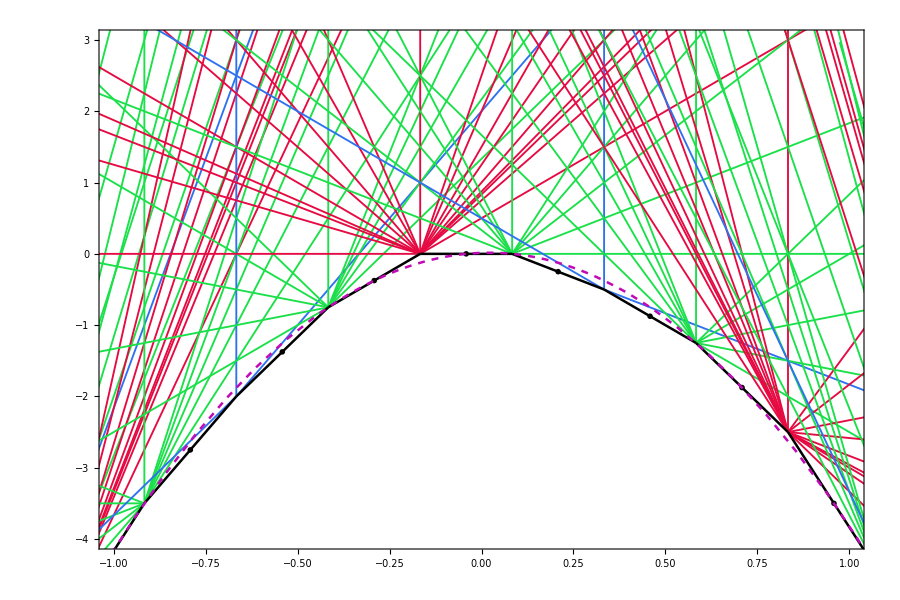

```mathematica
With[{mu=-1/6,  L=4,len=20},
Show[
Graphics[{
Table[XYFanRays[-ch[[k]]/.repCh,ch[[k+1]]/.repCh, mu], {k,1, Length[ch]-1}]
}],
Graphics[{Thickness[.002],lines[mu], labels[mu]}],
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotStyle->Directive[RGBColor[0.752, 0.038, 0.708], Dashed,Thickness[.002]]
],
PlotRange->{{-1,1},{-4,3}},
PlotRangeClipping->True,
AspectRatio->2/3,
Axes->False,
Frame->True,
ImageSize->900
]
]
```